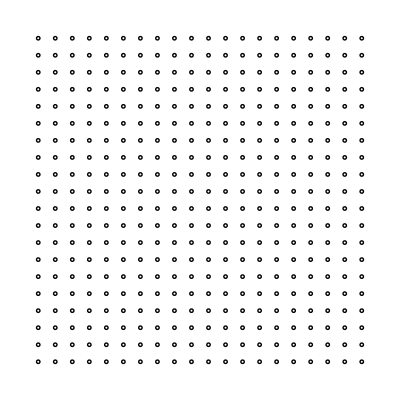

```mathematica
Clear[data]
data=Import["/Users/jiahaozhang/Documents/homework/mse561/assignmenttwo/atominfo.txt","Table"];
cicleall=Table[{{data[[i,1]],data[[i,2]]},data[[i,3]]},{i,1,Length[data]}];
rule=Circle@@cicleall[[#]]&;
c=Table[rule[i],{i,1,Length[cicleall]}];
Show[Graphics/@c]
```